```mathematica
Clear[p,f,x,w]
```

```mathematica
(* modulo two pattern Sierpinski gasket fractal pattern:odd-odd*)
```

```mathematica
p={-1-3 x-x^2+x^3,-1-x-5 x^2+x^3,1-11 x-11 x^2+x^3}
```

{-1-3 x-x^2+x^3,-1-x-5 x^2+x^3,1-11 x-11 x^2+x^3}

```mathematica
Table[x/.NSolve[p[[i]]==0,x],{i,Length[p]}]
```

{{-1.,-0.414214,2.41421},{-0.113936-0.422257 ⅈ,-0.113936+0.422257 ⅈ,5.22787},{-1.,0.0839202,11.9161}}

```mathematica
w=Table[x/.NSolve[p[[i]]==0,x][[3]],{i,Length[p]}]
```

{2.41421,5.22787,11.9161}

```mathematica
f[x_]=Fit[w,{1,x},x]
```

-2.98248+4.75093 x

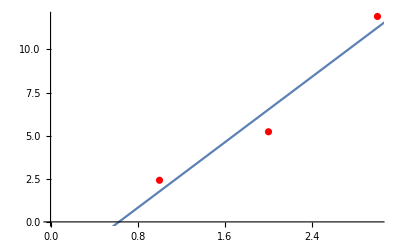

```mathematica
Show[ListPlot[w,PlotStyle->Red],Plot[f[x],{x,0,9}]]
```